# Projecto TAFC

```mathematica
ClearAll["Global`*"]
ClearAll[Derivative]
```

### Definição de variáveis

```mathematica
l[i_,t_]:=√((x[t]-xtoe[i])^2+(y[t]-ytoe[i])^2)
F[i_,t_]:=k(l0-l[i,t])
```

### Fase 1 - Suporte único

```mathematica
f1x=F[1,t]/m(x[t]-xtoe[1])/l[1,t]
f1y=F[1,t]/m(y[t]-ytoe[1])/l[1,t]-g
```

(k (x[t]-xtoe[1]) (l0-√((x[t]-xtoe[1])^2+(y[t]-ytoe[1])^2)))/(m √((x[t]-xtoe[1])^2+(y[t]-ytoe[1])^2))

-g+(k (l0-√((x[t]-xtoe[1])^2+(y[t]-ytoe[1])^2)) (y[t]-ytoe[1]))/(m √((x[t]-xtoe[1])^2+(y[t]-ytoe[1])^2))

### Fase 2 -Duplo suporte

```mathematica
f2x=F[1,t]/m(x[t]-xtoe[1])/l[1,t]+F[2,t]/m(x[t]-xtoe[2])/l[2,t]
f2y=F[1,t]/m(y[t]-ytoe[1])/l[1,t]+F[2,t]/m(y[t]-ytoe[2])/l[2,t]-g
```

(k (x[t]-xtoe[1]) (l0-√((x[t]-xtoe[1])^2+(y[t]-ytoe[1])^2)))/(m √((x[t]-xtoe[1])^2+(y[t]-ytoe[1])^2))+(k (x[t]-xtoe[2]) (l0-√((x[t]-xtoe[2])^2+(y[t]-ytoe[2])^2)))/(m √((x[t]-xtoe[2])^2+(y[t]-ytoe[2])^2))

-g+(k (l0-√((x[t]-xtoe[1])^2+(y[t]-ytoe[1])^2)) (y[t]-ytoe[1]))/(m √((x[t]-xtoe[1])^2+(y[t]-ytoe[1])^2))+(k (l0-√((x[t]-xtoe[2])^2+(y[t]-ytoe[2])^2)) (y[t]-ytoe[2]))/(m √((x[t]-xtoe[2])^2+(y[t]-ytoe[2])^2))

### Runge-Kutta 4^aordem

```mathematica
(*parametros numéricos e condições iniciais*)
(*se quisermos carregar os dados de um ficheiro*)
SetDirectory["/home/nteixeira/S1_2018_2019/PMEFT/TAFC/"]
T2=Import["fixed_points/invelocity.dat","Table","FieldSeparators"->","]
a=2363
params={k->14000,g->9.81,m->80,l0->1.0,Energy->T2[[a]][[1]]};
(*params={k->14000,g->9.81,m->80,l0->1.0,Energy->816}*)
l0=l0/.params;
f1nx=f1x/.{x[t]->xn[i],y[t]->yn[i]}/.params;
f2nx=f2x/.{x[t]->xn[i],y[t]->yn[i]}/.params;
f1ny=f1y/.{x[t]->xn[i],y[t]->yn[i]}/.params;
f2ny=f2y/.{x[t]->xn[i],y[t]->yn[i]}/.params;
(*Posição Inicial do CoM no eixo x*)
xn[0]=0;
(*Inicialização do calcanhar*)
xtoe[1]=0;
ytoe[1]=0;

(*Ângulo de Touchdown, ângulo de ataque, é o ângulo ao qual chegada a posição l0 Sin [θcrit] troca-se de single para double support*)
θcrit=Part[T2[[a]],2];
(*θcrit=73/180*π*)
(*começamos com single support*)
cases=1;
(*Parametros numéricos*)
Nmax=13000;
Δt =0.00050;

(*Parametros a mudar*)

(*Altura inicial da perna*)
yn[0]=T2[[a]][[3]];

(*Velocidade, obtida da energia*)
v=√(2/m(Energy-m g yn[0] - k/2(l0-yn[0])^2))/.params
(*ângulo da velocidade*)
α0=0;
xn'[0]=v Cos[α0];
yn'[0]=v Sin[α0];

For[i=0;step=0;L1={0};stepMAX=10,i<=Nmax,i++,
If[Mod[i,IntegerPart[0.25Nmax]]==0,Print[N[i/Nmax 100]]];
(*Suporte Único*)
(* Runge kutta para as velocidades*)
(*Vx*)
If[cases==1,
forçax[i]=f1nx;
K1vx=f1nx;
K2vx=f1nx/.{xn[i]->xn[i]+0.5 Δt K1vx,yn[i]->yn[i]+0.5Δt K1vx};
K3vx=f1nx/.{xn[i]->xn[i]+0.5 Δt K2vx,yn[i]->yn[i]+0.5Δt K2vx};
K4vx=f1nx/.{xn[i]->xn[i]+ Δt K3vx,yn[i]->yn[i]+Δt K3vx};
xn'[i+1]=xn'[i]+Δt/6(K1vx+2K2vx+2K3vx+K4vx);

(*Vy*)
forçay[i]=f1ny;
K1vy=f1ny;
K2vy=f1ny/.{xn[i]->xn[i]+0.5 Δt K1vy,yn[i]->yn[i]+0.5Δt K1vy};
K3vy=f1ny/.{xn[i]->xn[i]+0.5 Δt K2vy,yn[i]->yn[i]+0.5Δt K2vy};
K4vy=f1ny/.{xn[i]->xn[i]+ Δt K3vy,yn[i]->yn[i]+Δt K3vy};
yn'[i+1]=yn'[i]+Δt/6(K1vy+2K2vy+2K3vy+K4vy);


(*Runge kutta para as posições*)
(*X*)
K1x=xn'[i];
K2x=xn'[i]+0.5Δt K1x;
K3x=xn'[i]+0.5 Δt K2x;
K4x=xn'[i]+Δt K3x;

xn[i+1]=xn[i]+Δt/6(K1x+2K2x+2K3x+K4x);
(*Y*)
K1y=yn'[i];
K2y=yn'[i]+0.5Δt K1y;
K3y=yn'[i]+0.5 Δt K2y;
K4y=yn'[i]+Δt K3y;

yn[i+1]=yn[i]+Δt/6(K1y+2K2y+2K3y+K4y)];
(*Suporte Duplo*)

(* Runge kutta para as velocidades*)
(*Vx*)
If[cases==2,
forçax[i]=f2nx;
G1vx=f2nx;
G2vx=f2nx/.{xn[i]->xn[i]+0.5 Δt G1vx,yn[i]->yn[i]+0.5Δt G1vx};
G3vx=f2nx/.{xn[i]->xn[i]+0.5 Δt G2vx,yn[i]->yn[i]+0.5Δt G2vx};
G4vx=f2nx/.{xn[i]->xn[i]+ Δt G3vx,yn[i]->yn[i]+Δt G3vx};
xn'[i+1]=xn'[i]+Δt/6(G1vx+2G2vx+2G3vx+G4vx);

(*Vy*)
G1vy=f2ny;
G2vy=f2ny/.{xn[i]->xn[i]+0.5 Δt G1vy,yn[i]->yn[i]+0.5Δt G1vy};
G3vy=f2ny/.{xn[i]->xn[i]+0.5 Δt G2vy,yn[i]->yn[i]+0.5Δt G2vy};
G4vy=f2ny/.{xn[i]->xn[i]+ Δt G3vy,yn[i]->yn[i]+Δt G3vy};
yn'[i+1]=yn'[i]+Δt/6(G1vy+2G2vy+2G3vy+G4vy);

(*Runge kutta para as posições*)
(*X*)
G1x=xn'[i];
G2x=xn'[i]+0.5Δt G1x;
G3x=xn'[i]+0.5 Δt G2x;
G4x=xn'[i]+Δt G3x;

xn[i+1]=xn[i]+Δt/6(G1x+2G2x+2G3x+G4x);
(*Y*)
G1y=yn'[i];
G2y=yn'[i]+0.5Δt G1y;
G3y=yn'[i]+0.5 Δt G2y;
G4y=yn'[i]+Δt G3y;

yn[i+1]=yn[i]+Δt/6(G1y+2G2y+2G3y+G4y)];

(*transição single support para double support*)
If[cases==1 &&yn'[i]<0&& yn[i]<=l0 Sin[θcrit]&&yn[i-1]>l0 Sin[θcrit] && caso[i-1]≠2,

cases=2;
xtoe[2]=xn[i]+l0 Cos[θcrit];
ytoe[2]=0];

(*transição de double support para single support*)
If[cases==2 &&  √((xn[i]-xtoe[1])^2+(yn[i]-ytoe[1])^2)≥l0 (*||√((xn[i]-xtoe[2])^2+(yn[i]-ytoe[2])^2)≥l0*), 
xtoe[1]=xtoe[2];
ytoe[1]=ytoe[2];
cases=1];

caso[i]=cases;
xtoe1i[i]=xtoe[1];
xtoe2i[i]=xtoe[2];
If[(xn[i]-xtoe1i[i])>0&&(xn[i-1]-xtoe1i[i-1])<0&&caso[i]==1 &&caso[i-1]!=2 ,
L1=Join[L1,{i}];
step=step+1];
If[step==stepMAX ,
istepmax=i;
Break[]];

]
Length[L1]-1
```

/home/nteixeira/Desktop/S1_2018_2019/PMEFT/TAFC

{{Energia,Ang_TD,Pos_ini(y),x0'},{800.,1.08909,0.977241,0.00085827},{800.,1.08909,0.981793,0.000824558},{800.,1.11003,0.958285,0.000945951},8187,{840.,1.31947,0.998743,0.00118566},{840.,1.31947,1.,0.00117532},{840.,1.34041,0.997886,0.00119252},{840.,1.34041,0.998943,0.00118404}}
 |  |  |  |

2363

1.10212

0.

25.

50.

10

```mathematica
istepmax
```

7699

```mathematica
nlinhas=15;
Rugo[xkezd_,ykezd_,xveg_,yveg_]:={
hx=xveg-xkezd;hy=yveg-ykezd;szel=l0/(3*20);veghossz= l0/3.5;
hossz=√(hx^2+hy^2);
dh=(hossz-2*veghossz)/nlinhas;
{xkezd,ykezd}}~Join~{{xkezd+hx*(dh+veghossz)/hossz,ykezd+hy*(dh+veghossz)/hossz}}~Join~Table[If[OddQ[i],{xkezd+hx*(i*dh+veghossz)/hossz+hy*szel/hossz,ykezd+hy*(i*dh+veghossz)/hossz-hx*szel/hossz},
{xkezd+hx*(i*dh+veghossz)/hossz-hy*szel/hossz,ykezd+hy*(i*dh+veghossz)/hossz+hx*szel/hossz}],{i,2,nlinhas-2}]~Join~{{xkezd+hx*((nlinhas-1)*dh+veghossz)/hossz,ykezd+hy*((nlinhas-1)*dh+veghossz)/hossz}}~Join~{{xveg,yveg}}
```

7699

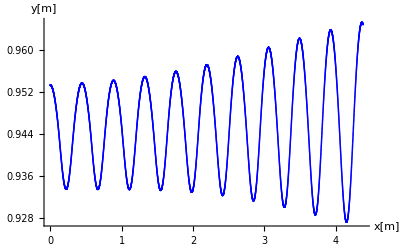

```mathematica
Nmax1= Part[L1,Length[L1]]
Show[ListPlot[Table[{xn[i],yn[i]},{i,0,Nmax1}],PlotStyle->Blue],(*ListPlot[Table[{i,caso[i]},{i,0,Nmax}],PlotStyle->Red],*)PlotRange->All,Axes->True,Axes->True,AxesLabel->{"x[m]","y[m]"}]
```

```mathematica
Nmax
forçay[500]
```

13000

forçay[500]

```mathematica
Length[L1]
xtoe1i[istepmax-1]
```

11

4.38435

```mathematica
Manipulate[Show[Evaluate[If[caso[j]==2, Graphics[Line[Rugo[xtoe2i[j],0,xn[j],yn[j]]]]]]/.Null->Sequence[],Graphics[Line[Rugo[xtoe1i[j],0,xn[j],yn[j]]]],ListPlot[Table[{xn[i],yn[i]},{i,0,j}]],Graphics[Disk[{xn[j],yn[j]},0.01]],PlotRange->All(*{{0, Max[Table[{xn[i]},{i,0,Nmax1}]]},{0,1.0}}*)],{j,0,Nmax1,1}]
```